```mathematica
The Kuramoto model
```

Kuramoto model The

-Graphics-

如上图所示，此为Kuramoto的动力学方程，不难看出方程由多个振子耦合而成，为了讨论方便，这里K值取相同值，取N=100.

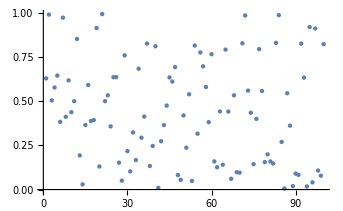

```mathematica
n=100;(*总的振子数*)
wset=Table[Subscript[w, i]=RandomReal[],{i,1,n}];(*设定振子的角频率*)
ListPlot[wset](*振子的角频率的分布*)
```

上图显示了振子的角频率的随机的！！

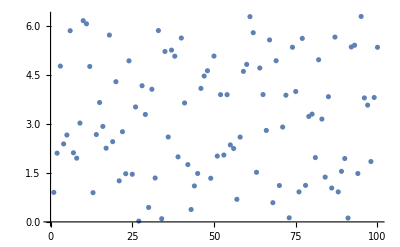

```mathematica
ioset=Table[Subscript[io, i]=2Pi*RandomReal[],{i,1,n}];(*设定初始相位*)
ListPlot[ioset](*振子的初始相位的分布*)
```

上图显示了振子的相位的随机的！！

```mathematica
Clear[k];
```

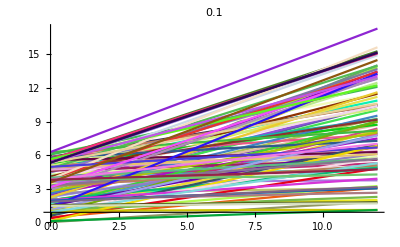
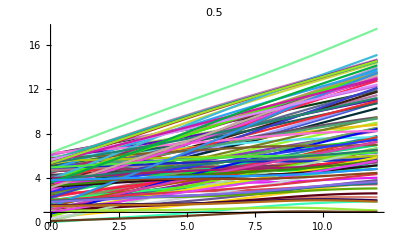
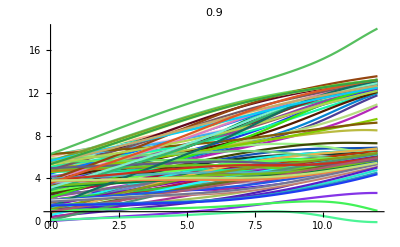
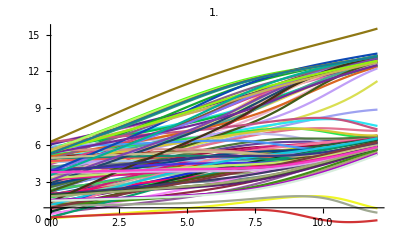
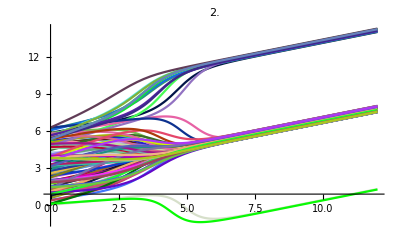
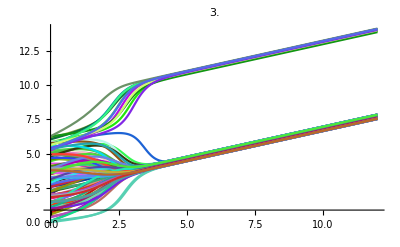
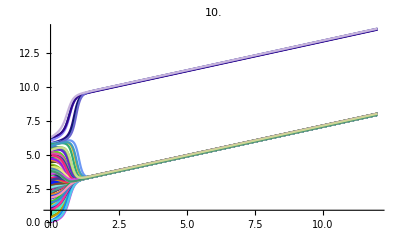

```mathematica
Table[(*设定K值,取: 0.1, 0.5, 0.9, 1.0, 2.0, 3.0, 10.0*)
eqg=Table[Subscript[o, i]'[t]==Subscript[w, i]-k/n Sum[Sin[Subscript[o, i][t]-Subscript[o, j][t]],{j,1,n}],{i,1,n}];(*方程组*)
init=Table[Subscript[o, i][0]==Subscript[io, i],{i,1,n}];(*初始条件*)
var=Table[Subscript[o, i],{i,1,n}];(*变量组*)
res=NDSolve[{eqg,init},var,{t,0,20}];(*求解方程组*)
Table[Subscript[oo, i]=Subscript[o, i]/.res[[1]],{i,1,n}];(*赋值*)
Show[Table[Plot[Subscript[oo, i][t],{t,0,12},PlotStyle->RandomColor[],PlotRange->All],{i,1,n}],PlotLabel->k]


,{k,{0.1, 0.5, 0.9, 1.0, 2.0, 3.0, 10.0}}](*绘制结果*)
```

如上图所示，在100个振子的角频率和相位都是随机的情况下，当k从小逐步变大时，出现同步相变，即振子的相位趋同！！
可以定义如下的序参量，从而更好观察到相变：
-Graphics-
下面绘制序参量随时间的变化，可以观察到K增加到0.7左右，序参量不再出现之前的震荡模式，而是达到稳定的1，说明发生了相变，即同步相变！！

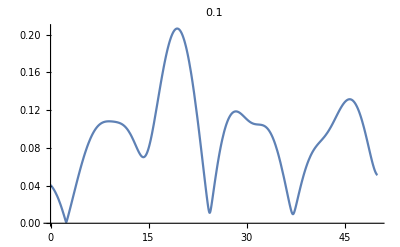
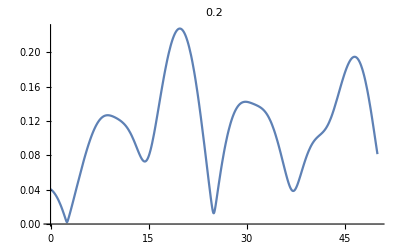
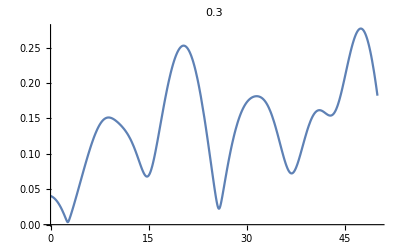
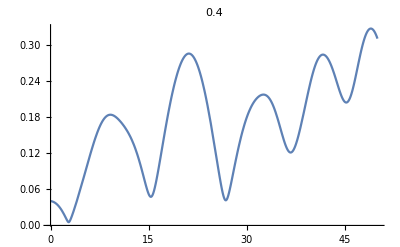
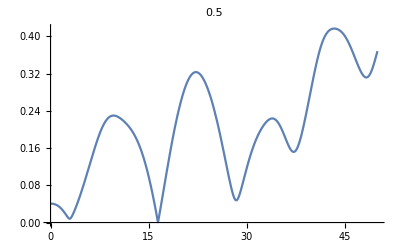
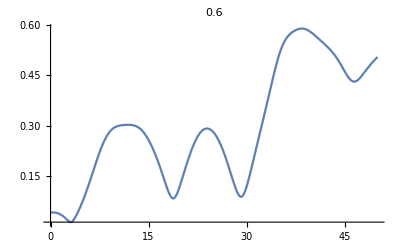
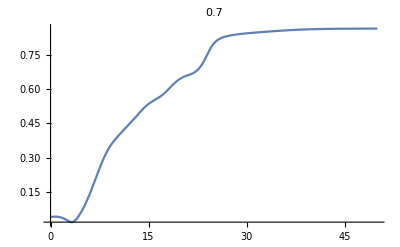
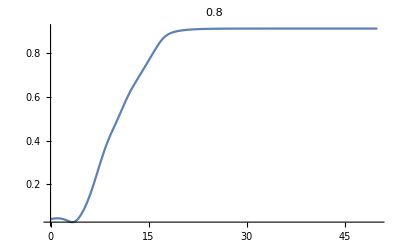

```mathematica
Table[(*设定K值,取: 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1.0, 2.0, 10*)
eqg=Table[Subscript[o, i]'[t]==Subscript[w, i]-k/n Sum[Sin[Subscript[o, i][t]-Subscript[o, j][t]],{j,1,n}],{i,1,n}];(*方程组*)
init=Table[Subscript[o, i][0]==Subscript[io, i],{i,1,n}];(*初始条件*)
var=Table[Subscript[o, i],{i,1,n}];(*变量组*)
res=NDSolve[{eqg,init},var,{t,0,50}];(*求解方程组*)
Table[Subscript[oo, i]=Subscript[o, i]/.res[[1]],{i,1,n}];(*赋值*)
Plot[Abs[1/n Sum[Exp[I*Subscript[oo, i][t]],{i,1,n}]],{t,0,50},PlotRange->All,PlotLabel->k]
,{k,{0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1.0, 2.0, 10}}]
```